```mathematica
ode=y'[x]-y[x]+x^2-1==0
```

-1+x^2-y[x]+y'[x]==0

```mathematica
generalSolution=FullSimplify[DSolve[ode,y[x],x]]
```

{{y[x]→(1+x)^2+ⅇ^x C[1]}}

```mathematica
particularSolution=FullSimplify[DSolve[{ode,y[0]==0},y[x],x]]
```

{{y[x]→-ⅇ^x+(1+x)^2}}

```mathematica
ya[x_]:=y[x]/.particularSolution[[1]]
```

```mathematica
FullSimplify[D[ya[x],x]]
```

2-ⅇ^x+2 x

```mathematica
dyadx[x_]:=2(x+1)-ⅇ^x
```

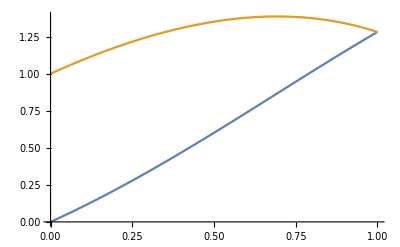

```mathematica
Plot[{ya[x],dyadx[x]},{x,0,1}]
```